```mathematica
Clear["Global`*"]
```

```mathematica
metaFile = FileNameJoin[{NotebookDirectory[],"output/gpu/meta.dat"}];
TcpuFile = FileNameJoin[{NotebookDirectory[],"output/cpu/T.dat"}];
TgpuFile = FileNameJoin[{NotebookDirectory[],"output/gpu/T.dat"}];
qcpuFile = FileNameJoin[{NotebookDirectory[],"output/cpu/q.dat"}];
qgpuFile = FileNameJoin[{NotebookDirectory[],"output/gpu/q.dat"}];
xFile = FileNameJoin[{NotebookDirectory[],"output/gpu/x.dat"}];
```

```mathematica
Lt = BinaryRead[metaFile, "UnsignedInteger32"]
wt = BinaryRead[metaFile, "UnsignedInteger32"]
Lx = BinaryRead[metaFile, "UnsignedInteger32"]
dx = BinaryRead[metaFile, "Real32"]
dtp = BinaryRead[metaFile, "Real32"]
Close[metaFile];
```

1024

1024

200

0.00502513

3.15649×10^-6

```mathematica
Tcpu = BinaryReadList[TcpuFile, "Real32"];
Tgpu = BinaryReadList[TgpuFile, "Real32"];
qcpu = BinaryReadList[qcpuFile, "Real32"];
qgpu = BinaryReadList[qgpuFile, "Real32"];
x = BinaryReadList[xFile, "Real32"];
```

```mathematica
Tcpu = ArrayReshape[Tcpu , {Lt, Lx}];
Tgpu = ArrayReshape[Tgpu , {Lt, Lx}];
qcpu = ArrayReshape[qcpu , {Lt, Lx}];
qgpu = ArrayReshape[qgpu , {Lt, Lx}];
```

```mathematica
qcpu[[;;,Lx]] = qcpu[[;;,Lx-1]];
qgpu[[;;,Lx]] = qgpu[[;;,Lx-1]];
```

```mathematica
(*qcpu[[;;,Lx]] = 1;
qgpu[[;;,Lx]] = 1;*)
```

```mathematica
P = Lx - 1
x = x[[Lx-P;;Lx-1]];
Tcpu= Tcpu[[;;,Lx-P;;Lx -1]];
Tgpu= Tgpu[[;;,Lx-P;;Lx - 1]];
qcpu= qcpu[[;;,Lx-P;;Lx -1]];
qgpu= qgpu[[;;,Lx-P;;Lx-1]];
```

199

```mathematica
Dimensions[qcpu]
```

{1024,199}

```mathematica
(*T$cpu = {};
T$gpu = {};
q$cpu = {};
q$gpu = {};
For[n=1,n <Lt, n=n++,
AppendTo[T$cpu,Transpose[{x,Tcpu[[n]]}]];
AppendTo[T$gpu,Transpose[{x,Tgpu[[n]]}]];
AppendTo[q$cpu,Transpose[{x,qcpu[[n]]}]];
AppendTo[q$gpu,Transpose[{x,qgpu[[n]]}]];
]*)
```

```mathematica
Manipulate[ListPlot[{Transpose[{x,Tgpu[[n]]}],Transpose[{x,qgpu[[n]]}]}, ImageSize->Large,Joined->True,PlotRange->Full],{n,1,Lt,1}]
```

```mathematica
Manipulate[ListPlot[{Transpose[{x,Tcpu[[n]]}],Transpose[{x,qcpu[[n]]}]}, ImageSize->Large,Joined->True,PlotRange->Full],{n,1,Lt,1}]
```

```mathematica
Manipulate[ListPlot[{Transpose[{x,Tcpu[[n]]}],Transpose[{x,Tgpu[[n]]}]}, ImageSize->Large, Joined->True, PlotRange->Full],{n,1,Lt,1}]
```

```mathematica
Manipulate[ListPlot[Transpose[{x,Tgpu[[n]] - Tcpu[[n]]}], ImageSize->Large],{n,1,Lt,1}]
```

{}

{0,0.125,0.25,0.5,1}

{1,39,78,155,310}

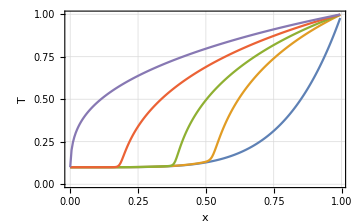

```mathematica
T$cpu = {};
T$gpu = {};
T$diff = {}
times = {0,0.125,0.25,0.5,1}
ind = IntegerPart[times/(dtp wt)] + 1
For[n=1,n ≤ Length[times] , n=n+1,
AppendTo[T$cpu,Transpose[{x,Tcpu[[ind[[n]]]]}]];
AppendTo[T$gpu,Transpose[{x,Tgpu[[ind[[n]]]]}]];
AppendTo[T$diff,Transpose[{x,Tgpu[[ind[[n]]]]-Tcpu[[ind[[n]]]]}]];
]
T1plt =ListLinePlot[T$cpu, PlotTheme->"Detailed",FrameLabel->{"x", "T"},ImageSize->Medium,Frame->True]
```

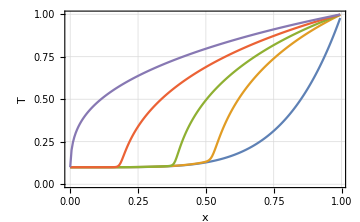

```mathematica
T2plt = ListLinePlot[T$gpu, PlotTheme->"Detailed",FrameLabel->{"x", "T"},ImageSize->Medium]
```

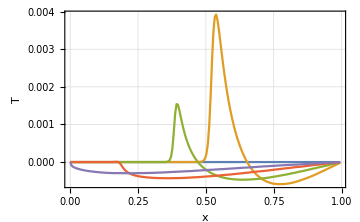

```mathematica
T3plt = ListLinePlot[T$diff, PlotTheme->"Detailed",PlotRange->Full,FrameLabel->{"x", "T"},ImageSize->Medium]
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"T1.pdf"}],T1plt]
Export[FileNameJoin[{NotebookDirectory[],"T2.pdf"}],T2plt]
Export[FileNameJoin[{NotebookDirectory[],"T3.pdf"}],T3plt]
```

/home/byrdie/School/Classes/PHSX565_AstrophysicalPlasmaPhysics/FinalProject/src/rempel_heat_conduction/T1.pdf

/home/byrdie/School/Classes/PHSX565_AstrophysicalPlasmaPhysics/FinalProject/src/rempel_heat_conduction/T2.pdf

/home/byrdie/School/Classes/PHSX565_AstrophysicalPlasmaPhysics/FinalProject/src/rempel_heat_conduction/T3.pdf